# Analysis of Packing V3E05L1N01T2_1

Three Vertices, Five Edges, 1 Loop, Combinatorial Number 01, Face Pattern 2, Type 1

-Graphics-

These are our labels for alpha and beta.  We use the exact same methods to find the coordinates that were used for V3E5L0N1T1_1.

We want the distance between w1 and w2 to be exactly 1 to get a self tangency:

```mathematica
Simplify[Sqrt[(( 2*Sqrt[2]/2*Sin[β/2]*Cos[Pi/2-α/2+ArcCos[2 (-1+√2)]+Pi/2-β/2])-(2*Sqrt[2]/2*Sin[α/2]))^2+(2*Sqrt[2]/2*Sin[β/2]*Sin[Pi/2-α/2+ArcCos[2 (-1+√2)]+Pi/2-β/2])^2]]
```

√(4-2 √2-Cos[α]-Cos[β]+Cos[α-ArcCos[2 (-1+√2)]]+Cos[β-ArcCos[2 (-1+√2)]]-Cos[α+β-ArcCos[2 (-1+√2)]])

```mathematica
Simplify[Solve[√(4-2 √2-Cos[α]-Cos[β]+Cos[α-ArcCos[2 (-1+√2)]]+Cos[β-ArcCos[2 (-1+√2)]]-Cos[α+β-ArcCos[2 (-1+√2)]])==1,β]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{β→-ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 √(Sin[α/2]^2 (218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α])))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]},{β→ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 √(Sin[α/2]^2 (218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α])))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]},{β→-ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]+2 √(Sin[α/2]^2 (218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α])))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]},{β→ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]+2 √(Sin[α/2]^2 (218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α])))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]}}

```mathematica
N[Simplify[Solve[√(4-2 √2-Cos[α]-Cos[β]+Cos[α-ArcCos[2 (-1+√2)]]+Cos[β-ArcCos[2 (-1+√2)]]-Cos[α+β-ArcCos[2 (-1+√2)]])==1,β]]/.α->.7]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{β→-1.78591},{β→1.78591},{β→-0.748772},{β→0.748772}}

Both angles can’t be acute, because that would cause circles to overlap.  Also, notice that there is symmetry between the first and second solutions; if β is negative then α will have a positive lower bound and then if β is positive then α will have a negative lower bound.  We will choose the second solution.

So {β→ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 √(Sin[α/2]^2 (218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α])))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]}}

## Circle Centers and Radii

```mathematica
centers = {{0,0},
{Sqrt[2]/2Cos[Pi/2-α/2],
Sqrt[2]/2Sin[Pi/2-α/2]},
{Sqrt[2]/2Cos[Pi/2-α/2+ArcCos[2(-1+√2)]],
Sqrt[2]/2Sin[Pi/2-α/2+ArcCos[2 (-1+√2)]]}}
```

{{0,0},{Sin[α/2]/(√2),Cos[α/2]/(√2)},{Sin[α/2-ArcCos[2 (-1+√2)]]/(√2),Cos[α/2-ArcCos[2 (-1+√2)]]/(√2)}}

## Lattice Vectors

We are working this flat torus

```mathematica
latticeVectors = {
 {2*Sqrt[2]/2*Sin[α/2],0},
{ 2*Sqrt[2]/2*Sin[(ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 √(Sin[α/2]^2 (218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α])))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))])/2]*Cos[Pi/2-α/2+ArcCos[2 (-1+√2)]+Pi/2-(ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 √(Sin[α/2]^2 (218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α])))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))])/2],2*Sqrt[2]/2*Sin[(ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 √(Sin[α/2]^2 (218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α])))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))])/2]*Sin[Pi/2-α/2+ArcCos[2 (-1+√2)]+Pi/2-(ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 √(Sin[α/2]^2 (218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α])))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))])/2]}};
```

## Edges

Here we store the edges a list {i,j,m,n} where center[[i]] is connected to center[[j]] + m*latticeVectors[[1]] + n*latticeVectors[2]]
center[[i]] is *always* in the fundamental domain ****the last two numbers are winding numbers****

```mathematica
edges = {{1,2,0,0},{1,3,0,0},{2,3,0,0},{3,1,0,1},{2,1,1,0}(*,{1,1,-1,1}*)};
```

### Check the edge lengths are all 2rs= Sqrt[2]-1 or rs+rb=Sqrt[2]rb=Sqrt[2]/2=1/Sqrt[2]

```mathematica
For[i=1,i≤Length[edges],i++,
P1:= centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]];
P2:= centers[[edges[[i,1]] ]];
Print["Edge ",i,": Length is ",
Sqrt[FullSimplify[(P1[[1]]-P2[[1]])^2+(P1[[2]]-P2[[2]])^2,{0≤α≤ Pi/2}]]];
]
```

Edge 1: Length is 1/(√2)

Edge 2: Length is 1/(√2)

Edge 3: Length is √(3-2 √2)

Edge 4: Length is 1/(√2)

Edge 5: Length is 1/(√2)

Note that we didn’t include the self-tangency from w1 to w2  because I didn’t know how to describe it in the edges, but our substitution of β guarantees such a self tangency.

Yes!

## Packing Visualization

Here we visualize the packing and the fundamental domain to help determine the value of the parameters for which this is a packing graph.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,Pi,"α"},ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)],π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]},AnimationRunning -> False
]
```

Our bounds are between when α = Pi and when β = Pi.  However, because of symetry we can examine when α = Pi.

```mathematica
Simplify[β==ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 √(Sin[α/2]^2 (218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α])))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]/.α->Pi]
```

β==ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)]

```mathematica
N[β==ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)]]
```

β==2.87868

```mathematica
Simplify[Solve[(2Pi-α)/2== ArcCos[((1/2)(Sqrt[2]-1))/((1/Sqrt[2]))]],α]
```

{{True→2 (π-ArcCos[1-1/(√2)])}}

However, our bounds are not ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)],Pi because these give us duplicate packings.  So we want to take half.

```mathematica
FullSimplify[(Pi-ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)])/2]
```

1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]

```mathematica
FullSimplify[Pi-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]]
```

π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]

## Locally Maximally Dense

We have to determine for which values of α and β the packing is locally maximally dense. To be locally maximally dense (Following Connelly, Rigid Circle and Sphere Packings, Page 51, Theorem 6.1)
	1. The packing graph is rigid as a bar framework
	2. Have a proper stress that is non-zero on every member

### Rigid as bar framework

To be rigid as a bar framework we need to establish a rigid ordering of the circles. The numbering of the circles in the picture above is a rigid ordering of the packing disks -- See Lemma 6.2 in the Connelly paper on Rigid Sphere and Circle Packings. Note: The first is held fixed.

### Proper Stress

Assign a scalar to each edge of the packing and collect those scalars in a vector called ω. We need to solve the linear algebra problem where the sum of the ω_i times the vector from vertex j is zero.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}},(*Angle Markers Labels*)
Table[Text[Style[Subscript["ω",i],Large,Red],1/2*(centers[[edges[[i,1]] ]]+centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]])/.{α->a,β->b}],{i,1,Length[edges]}](*Label Edges With Stresses*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,Pi,"α"},ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)],Pi},AnimationRunning -> False
]
```

```mathematica
equations = Table[{0,0},{k,Length[centers]}]; (*Start with the zero equations*)
w =Table[Subscript[ω,i],{i,Length[edges]}]; (*Initialize a vector of Subscript[ω, i]*)
For[i=1,i≤Length[centers], i++, (*i is the center number*)
For[j=1,j≤Length[edges], j++, (*j is the edge number*)
If[edges[[j,1]]==i, (*center i is the starting point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(centers[[edges[[j,1]] ]]-centers[[edges[[j,2]] ]]-
edges[[j,3]]*latticeVectors[[1]]-
edges[[j,4]]*latticeVectors[[2]])] 
If[edges[[j,2]]==i, (*center i is the ending point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(-centers[[edges[[j,1]] ]]+centers[[edges[[j,2]] ]]+
edges[[j,3]]*latticeVectors[[1]]+
edges[[j,4]]*latticeVectors[[2]])]
]
]
stresses = Flatten[Simplify[Solve[Flatten[equations]==Flatten[Table[{0,0},{k,Length[centers]}]],w]]]
```

{ω_1→0,ω_2→0,ω_3→0,ω_4→0,ω_5→0}

```mathematica
yuck := Simplify[equations /. stresses] (*check the solutions, Should output all zeros but I don't think Mathematica can simplify it*)
```

```mathematica
N[Simplify[yuck/.{α-> 5Pi/6,β-> 5Pi/6}]]
```

{{0.,0.},{0.,0.},{0.,0.}}

```mathematica
guts := Simplify[Union[{0},Table[Subscript[ω, i]/.stresses,(*first list all of the right hand sides of all the stresses*)
{i,Length[edges]}]/.Subscript[ω, 1]->1]]
```

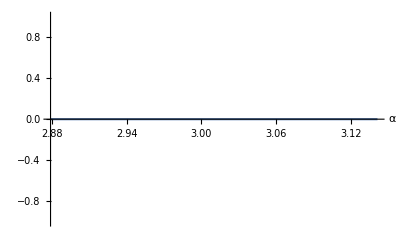

```mathematica
Plot[guts,{α,ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)],Pi},AxesLabel->Automatic]
```

## Moduli Space Of Locally Maximally Dense Packings

Determine the Torus Angle and Ratio for the packings that are locally maximally dense.

```mathematica
torusAngleFromVectors = Simplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]],{Element[{α},Reals],ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)]<α<π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]}]
```

ArcCos[-((Cos[1/2 (α-2 ArcCos[2 (-1+√2)]+Conjugate[ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 Sin[α/2] √(218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α]))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]])] Sin[1/2 Conjugate[ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 Sin[α/2] √(218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α]))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]]])/(√(Abs[Cos[1/2 (α-2 ArcCos[2 (-1+√2)]+ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 Sin[α/2] √(218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α]))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))])] Sin[1/2 ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 Sin[α/2] √(218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α]))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]]]^2+Abs[Sin[1/2 ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 Sin[α/2] √(218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α]))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]] Sin[1/2 (α-2 ArcCos[2 (-1+√2)]+ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 Sin[α/2] √(218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α]))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))])]]^2)))]

```mathematica
torusRatio = Simplify[EuclideanDistance[{0,0},latticeVectors[[2]]]/EuclideanDistance[{0,0},latticeVectors[[1]]],{Element[{α},Reals],ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)]<α<π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]}]
```

√(Abs[Cos[1/2 (α-2 ArcCos[2 (-1+√2)]+ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 Sin[α/2] √(218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α]))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))])] Sin[1/2 ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 Sin[α/2] √(218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α]))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]]]^2+Abs[Sin[1/2 ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 Sin[α/2] √(218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α]))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))]] Sin[1/2 (α-2 ArcCos[2 (-1+√2)]+ArcCos[(37-26 √2+(-62+44 √2) Cos[α]+(25-18 √2) Cos[2 α]+12 √(-11+8 √2) Sin[α]-8 √(-22+16 √2) Sin[α]-5 √(-11+8 √2) Sin[2 α]+4 √(-22+16 √2) Sin[2 α]-2 Sin[α/2] √(218-152 √2+2 (-598+423 √2) Cos[α]-56 (-41+29 √2) Cos[2 α]-1270 Cos[3 α]+898 √2 Cos[3 α]+253 √(-11+8 √2) Sin[α]-174 √(-22+16 √2) Sin[α]-486 √(-11+8 √2) Sin[2 α]+344 √(-22+16 √2) Sin[2 α]+269 √(-11+8 √2) Sin[3 α]-190 √(-22+16 √2) Sin[3 α]))/(2 (7-4 √2+(-6+4 √2) Cos[α]+2 √(-11+8 √2) Sin[α]))])]]^2) Csc[α/2]

Now plot the region of the moduli space that is covered by (r,theta)=(torusRatio,torusAngle). The right boundary is in the region, the others are not.

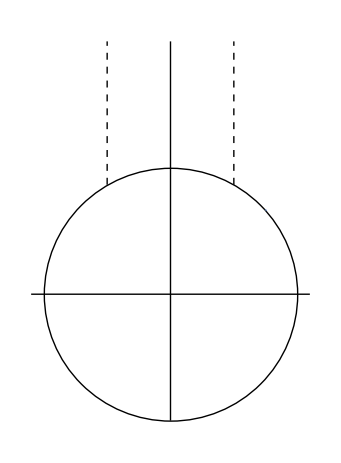

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{torusRatio*Cos[torusAngleFromVectors],torusRatio*Sin[torusAngleFromVectors]},{α,ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)],π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]}]
]
```

Now, we can reflect this region and then invert it to place it into the region in the moduli space.

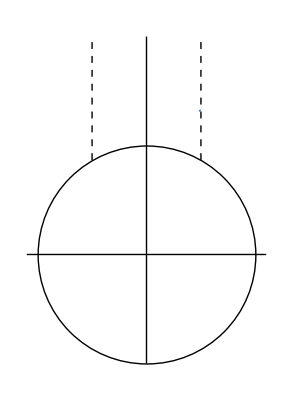

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{(-torusRatio*Cos[torusAngleFromVectors]+1)/
((-torusRatio*Cos[torusAngleFromVectors]+1)^2+(torusRatio*Sin[torusAngleFromVectors])^2)
,(torusRatio*Sin[torusAngleFromVectors])/
((-torusRatio*Cos[torusAngleFromVectors]+1)^2+(torusRatio*Sin[torusAngleFromVectors])^2)},{α,ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)],π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]}]
]
```

## Density Of Packings

Here we analyze the density of the locally maximally dense packings and explore the density.

```mathematica
torusDensity = Simplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ,{Element[{α},Reals],ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)]<α<π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]}]
```

$Aborted

Plot the density over the parameter space

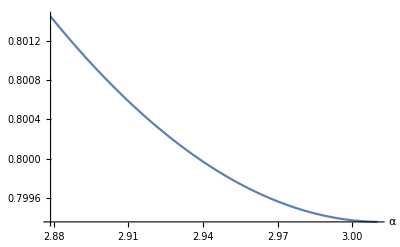

```mathematica
Plot[torusDensity,{α,ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)],π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]},AxesLabel->Automatic]
```

Color the moduli space region with color depending on the density. Red shade is close to 1 and Blue shade is close to .5

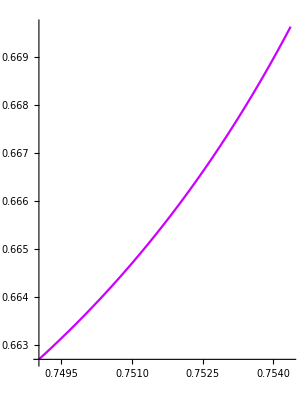

```mathematica
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)],π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]},ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None]
```

Now find the minimum and maximum density with in the region

```mathematica
NMinimize[{torusDensity,ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)]< α && α <π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]},{{α,ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)],π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.7993573088212865619523517675522021582078,{α→3.010134248647178984085199736711402488663}}

```mathematica
NMaximize[{torusDensity,ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)]< α && α <π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]},{{α,ArcCos[(2 (-31+22 √2+√(1245-880 √2)))/(-13+8 √2)],π-1/2 ArcCos[2/41 (-51+38 √2+√(5 (737-480 √2)))]}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.8014446723007539671949097258930182839285,{α→2.878675843704564730503317759135146630172}}